# Mathématica 3

## La fonction Nest

```mathematica
Quit[]
```

```mathematica
Nest[f,x0,3]
```

f[f[f[x0]]]

```mathematica
NestList[f,x0,3]
```

{x0,f[x0],f[f[x0]],f[f[f[x0]]]}

```mathematica
f[x_]:=(x+2/x)/2
```

```mathematica
NestList[f,1,4]
```

{1,3/2,17/12,577/408,665857/470832}

```mathematica
NestList[f,1.,4]
```

{1.,1.5,1.41667,1.41422,1.41421}

```mathematica
f1[{x_,y_}]:=List[{(x+y)/2,Sqrt[x*y]}]
```

```mathematica
f1[{5,1}]
```

{{3,√5}}

```mathematica
NestList[f1,{a,b},4]
```

{{a,b},{{(a+b)/2,√(a b)}},f1[{{(a+b)/2,√(a b)}}],f1[f1[{{(a+b)/2,√(a b)}}]],f1[f1[f1[{{(a+b)/2,√(a b)}}]]]}

```mathematica
NestList[f1,{12,10},5]
```

{{12,10},{{11,2 √30}},f1[{{11,2 √30}}],f1[f1[{{11,2 √30}}]],f1[f1[f1[{{11,2 √30}}]]],f1[f1[f1[f1[{{11,2 √30}}]]]]}

```mathematica
f2[x_,n_]:=List[x+n/x,n+1]
```

```mathematica
f2'[n_]:=NestList[f2,{x,1},n]
```

```mathematica
f2'[4]
```

{{x,1},f2[{x,1}],f2[f2[{x,1}]],f2[f2[f2[{x,1}]]],f2[f2[f2[f2[{x,1}]]]]}

```mathematica
fib[{a_,b_}]:=List[b,a+b]
```

```mathematica
fibo[n_]:=NestList[fib,{1,1},n]
```

```mathematica
fibo[7]
```

{{1,1},{1,2},{2,3},{3,5},{5,8},{8,13},{13,21},{21,34}}

## Exercices divers, au choix

```mathematica
α[x_]:=Floor[x+1/2]
```

```mathematica
δ[x_]:=Abs[x-α[x]]
```

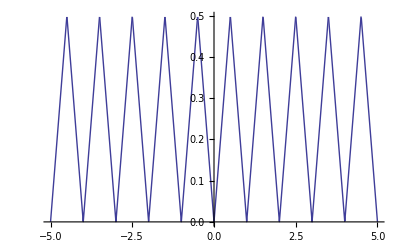

```mathematica
Plot[δ[x],{x,-5,5}]
```

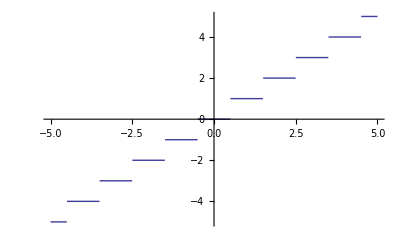

```mathematica
Plot[α[x],{x,-5,5}]
```

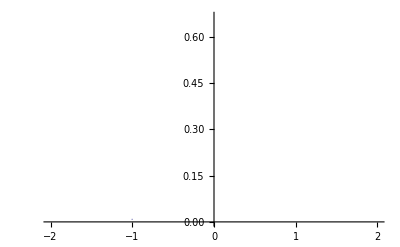

```mathematica
Plot[Sum[δ[2^(k)*x]/2^k,{k,0,20}],{x,-2,2}]
```

```mathematica
Sum[δ[2^(k)*x]/2^k,{k,0,n}]
```

∑_(k=0)^n 2^-k Abs[2^k x-Floor[1/2+2^k x]]

```mathematica
RandomInteger[541543515435468489]
```

534918099669308262

```mathematica
hasard[p_,n_]:=Module[{l1=Range[n],l2={}},
Do[
RandomInteger[n],

;l2]
```

```mathematica
hasard[50,15]
```

```mathematica
Clear[hasard]
```

```mathematica
Table[PrimeQ[n^5+n^4+1],{n,0,10}]
```

{False,True,False,False,False,False,False,False,False,False,False}

```mathematica
PrimeQ[n^5+n^4+1]
```

False

```mathematica
Factor[n^5+n^4+1]
```

(1+n+n^2) (1-n+n^3)